# Cellular Automaton

## 2D Cellular Automaton

```mathematica
CellularAutomaton[{14, 4, 1},0]
```

CellularAutomaton::initn: The initial condition specification 0 should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 3.

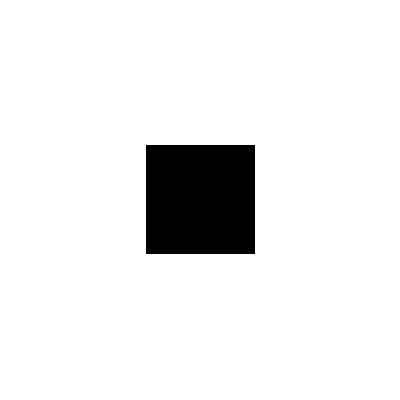

```mathematica
Manipulate[First[CellularAutomaton[{4566,{4,1},{1,1}},{{{1}},0},100]],{i,0,100}]
```